```mathematica
SetDirectory@NotebookDirectory[]
Import["esmlib_nsl.wl"]
```

/home/eric/git/nonlinear-systems-lab

```mathematica
ClearAll[logistic]
logistic[x_]:=r x (1 - x)
```

## Fixed Points

```mathematica
plotLogistic[logistic_,rr_]:=
Module[{sol},
Grid[{
{"r=",r},
{Show[Plot[logistic[x]/.r->rr,{x,0,1},PlotRange->{0,1}],Plot[x,{x,0,1}]],SpanFromLeft},
{"Intersections",sol=Solve[x==logistic[x],x]},
{"Slopes",Table[Evaluate[D[logistic[x],x]]/.s,{s,sol}]}

}/.r->rr,
Frame->All]]
```

```mathematica
Manipulate[plotLogistic[logistic,r],{{r,3},0,5}]
```

## Cycles

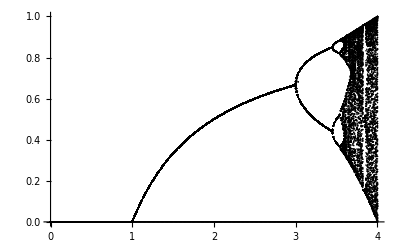

```mathematica
bifdiag=ListPlot[Table[Thread[{r,Nest[logistic,Range[0,1,0.005],200]}],{r,0,4,0.01}],PlotStyle->Black]
```

```mathematica
sols=Solve[Nest[logistic,x,2]==x,x]/.r->a;
Column[sols,Frame->All]
```

{x→0}
{x→(-1+a)/a}
{x→(a+a^2-a √(-3-2 a+a^2))/(2 a^2)}
{x→(a+a^2+a √(-3-2 a+a^2))/(2 a^2)}

```mathematica
Dynamic@Show[bifdiag,Table[Plot[x/.sol,{a,0,4},PlotStyle->Red],{sol,sols}]]
```

```mathematica
Manipulate[plotLogistic[Nest[logistic,#,3]&,r],{{r,3.},0,5}]
```